```mathematica
SetDirectory[NotebookDirectory[]];
```

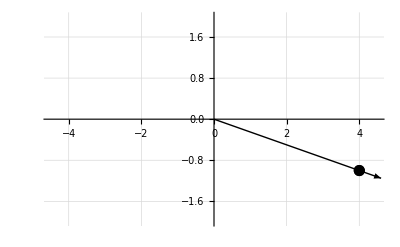

point.png

```mathematica
Show[
ListPlot[{{4,-1}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Arrow[{{0,0},1.15{4,-1}}]}],
PlotRange->{{-4.5,4.5},{-2,2}},GridLines->Automatic,AxesStyle->Directive[16]]
Export["point.png",%]
```

121 °

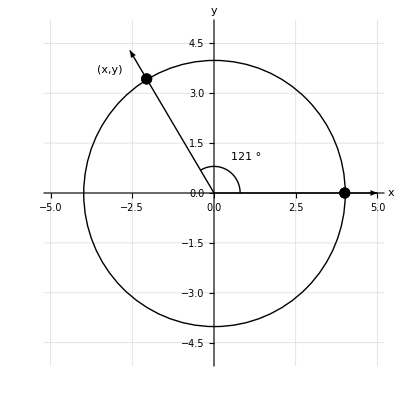

circle.png

```mathematica
r=4;
θ=121*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.6,(r+1) Sin[θ]-0.6}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[θ,Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],

PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export["circle.png",%]
```

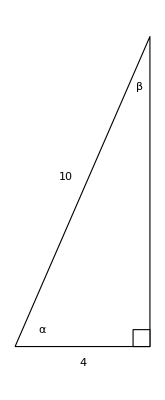

triangle1.png

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{4,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Text[Style[10,Large],{1.5,5}]}],
Graphics[{Text[Style[4,Large],{2,-0.5}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export["triangle1.png",%]
```

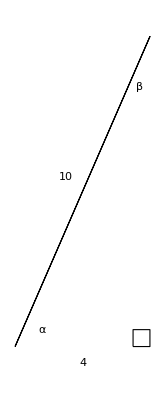

triangle2.png

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{7Cos[ArcSin[1]],0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Text[Style[10,Large],{1.5,5}]}],
Graphics[{Text[Style[4,Large],{2,-0.5}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export["triangle2.png",%]
```

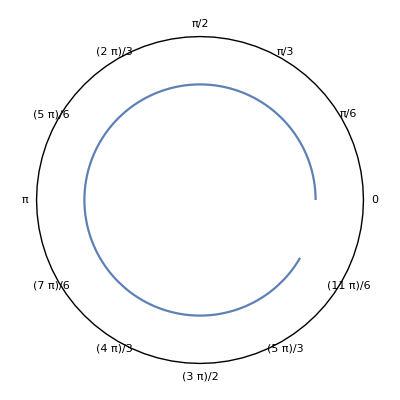

```mathematica
SetDirectory[NotebookDirectory[]];
```

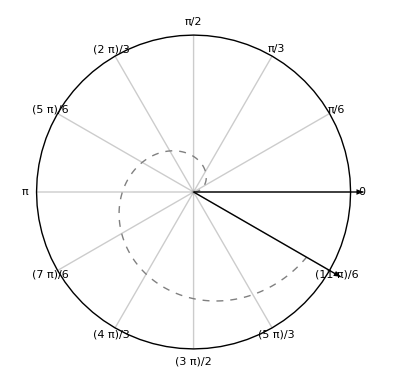

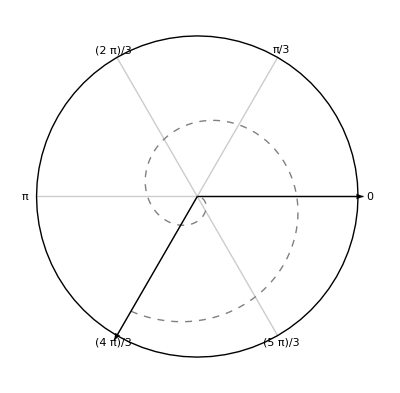

```mathematica
θ=11Pi/6;
Show[PolarPlot[{t/5},{t,0,θ},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/6,Pi/6}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/6,Pi/6}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ 1.5Cos[θ],1.5 Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{1.5,0}}]}]]
Export["ang1.png",%];

θ=-8Pi/3;
Show[PolarPlot[{-t/7},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},PolarTicks->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],Automatic},PolarGridLines->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},{ 1.5Cos[θ],1.5 Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{1.5,0}}]}]]
Export["ang2.png",%];
```

```mathematica
Drop[Table[i,{i,0,2 Pi,Pi/6}],-1]
```

{0,π/6,π/3,π/2,(2 π)/3,(5 π)/6,π,(7 π)/6,(4 π)/3,(3 π)/2,(5 π)/3,(11 π)/6}

```mathematica
Show[
Graphics[{EdgeForm[Thick],FaceForm[White],Triangle[{{0,0},{100,0},{10 Cos[ArcCos[4/10]],10 Sin[ArcCos[4/10]]}}]}],
Graphics[{EdgeForm[Thick],FaceForm[White],Rectangle[{3.5,0},{4,0.5}]}],
Graphics[{Text[Style[α,Large],{0.8,0.5}]}],
Graphics[{Text[Style[10,Large],{1.5,5}]}],
Graphics[{Text[Style[4,Large],{2,-0.5}]}],
Graphics[{Text[Style[β,Large],{10 Cos[ArcCos[4/10]]-0.3,10 Sin[ArcCos[4/10]]-1.5}]}]
]
Export["cell.png",%]
```

-Graphics-

cell.png

```mathematica
Tan[40*Degree]*100.
```

83.91

```mathematica
119-84
```

35

```mathematica
4Cos[121*Degree]//N
```

-2.06015

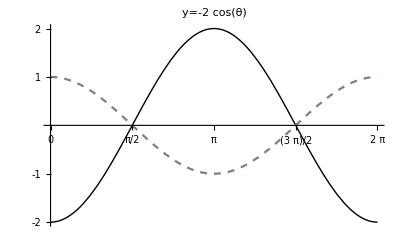

g1.png

```mathematica
Show[
Plot[-2Cos[t],{t,0,2Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
Ticks->{Table[k Pi/2,{k,0,4}],{-2,-1,1,2}},PlotLabel->HoldForm[y=-2Cos[θ]]]
Export["g1.png",%]
```

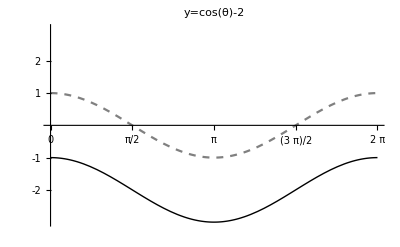

g2.png

```mathematica
Show[
Plot[Cos[t]-2,{t,0,2Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,2Pi},{-3,3}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/2,{k,0,4}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Cos[θ]-2]]
Export["g2.png",%]
```

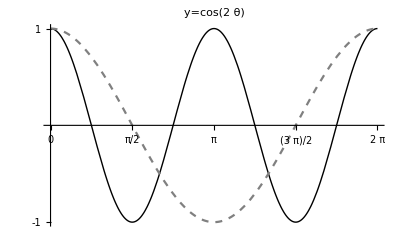

g3.png

```mathematica
Show[
Plot[Cos[2t],{t,0,2Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,2Pi},{-1,1}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/4,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Cos[2θ]]]
Export["g3.png",%]
```

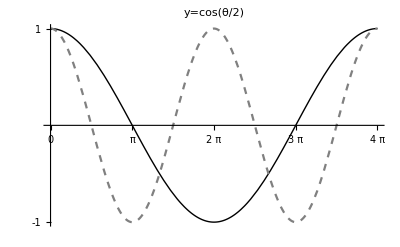

g4.png

```mathematica
Show[
Plot[Cos[t/2],{t,0,4Pi},PlotStyle->{Thick,Black}],
Plot[Cos[t],{t,0,4Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,4Pi},{-1,1}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/2,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Cos[θ/2]]]
Export["g4.png",%]
```

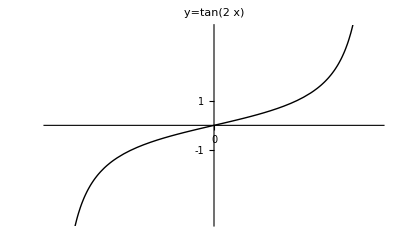

g5.png

```mathematica
Show[
Plot[Tan[2t],{t,-Pi/4,Pi/4},PlotStyle->{Thick,Black},ExclusionsStyle->{Dashed},Exclusions->{t==-Pi/4,t==Pi/4}],
PlotRange->{{-Pi/4,Pi/4},{-4,4}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/8,{k,-8,8}],{-1,1}},PlotLabel->HoldForm[y=Tan[2x]]]
Export["g5.png",%]
```

```mathematica
Solve[3t-Pi/4==2Pi]
```

{{t→(3 π)/4}}

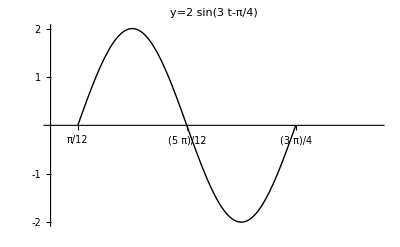

g6.png

```mathematica
Show[
Plot[2Sin[3t-Pi/4],{t,Pi/12,3Pi/4},PlotStyle->{Thick,Black}],
PlotRange->{{0,Pi},{-2,2}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/6+Pi/12,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=2Sin[3t-Pi/4]]]
Export["g6.png",%]
```

```mathematica
3Pi/4-Pi/12
```

(2 π)/3

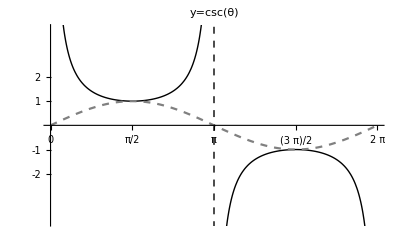

g7.png

```mathematica
Show[
Plot[Csc[t],{t,0,2Pi},PlotStyle->{Thick,Black},Exclusions->{t==Pi,t==2Pi},ExclusionsStyle->Dashed],
Plot[Sin[t],{t,0,2Pi},PlotStyle->{Gray,Dashed}],
PlotRange->{{0,2Pi},{-4,4}},AxesOrigin->{0,0},
Ticks->{Table[k Pi/4,{k,0,8}],{-2,-1,1,2}},PlotLabel->HoldForm[y=Csc[θ]]]
Export["g7.png",%]
```

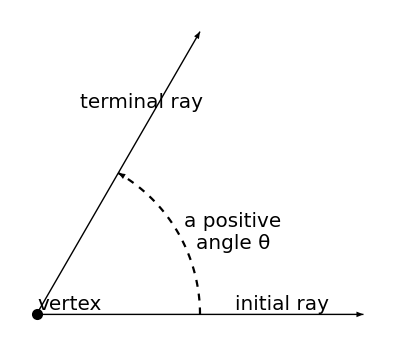

{positive-angle.pdf,positive-angle.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Graphics[Arrow[{{0,0},{Cos[Pi/3],Sin[Pi/3]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{Cos[t],Sin[t]}/2,{t,0,Pi/3},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Epilog->{Text[Style["a positive\nangle θ",20],{0.6,0.25}],
Text[Style["vertex",20],{0.1,0.03}],
Text[Style["initial ray",20],{0.75,0.03}],
Rotate[Text[Style["terminal ray",20],{0.32,0.65}],Pi/3]}
]
Export[{"positive-angle.pdf","positive-angle.svg"},%]
```

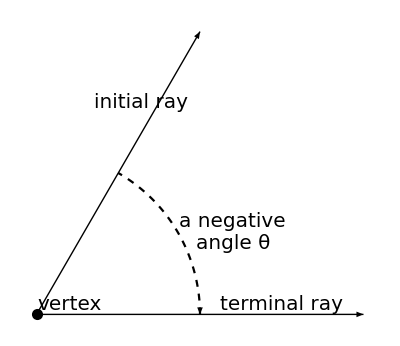

{negative-angle.pdf,negative-angle.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Graphics[Arrow[{{0,0},{Cos[Pi/3],Sin[Pi/3]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{Cos[t],Sin[t]}/2,{t,Pi/3,0},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{-0.05,0}],Arrow[x]],
Epilog->{Text[Style["a negative\nangle θ",20],{0.6,0.25}],
Text[Style["vertex",20],{0.1,0.03}],
Text[Style["terminal ray",20],{0.75,0.03}],
Rotate[Text[Style["initial ray",20],{0.32,0.65}],Pi/3]}
]
Export[{"negative-angle.pdf","negative-angle.svg"},%]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Graphics[Arrow[{{0,0},{Cos[Pi/3],Sin[Pi/3]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{Cos[t],Sin[t]}/2,{t,Pi/3,0},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{-0.05,0}],Arrow[x]],
Epilog->{Text[Style["a negative angle θ",16],{0.65,0.25}],
Text[Style["vertex",16],{0.1,0.03}],
Text[Style["terminal ray",16],{0.75,0.03}],
Rotate[Text[Style["initial ray",16],{0.32,0.65}],Pi/3]}
]
Export[{"negative-angle.pdf","negative-angle.svg"},%]
```

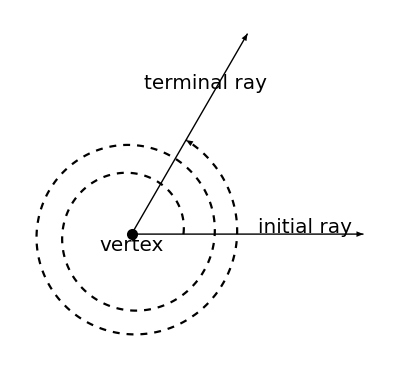

{intro-angle.pdf,intro-angle.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Graphics[Arrow[{{0,0},{Cos[Pi/3],Sin[Pi/3]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{Sqrt[t/20+0.2]Cos[t],Sqrt[t/20+0.2]Sin[t]}/2,{t,0,Pi/3+2Pi+2Pi},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Epilog->{
Text[Style["vertex",20],{0.0,-0.05}],
Text[Style["initial ray",20],{0.75,0.03}],
Rotate[Text[Style["terminal ray",20],{0.32,0.65}],Pi/3]}
]
Export[{"intro-angle.pdf","intro-angle.svg"},%]
```

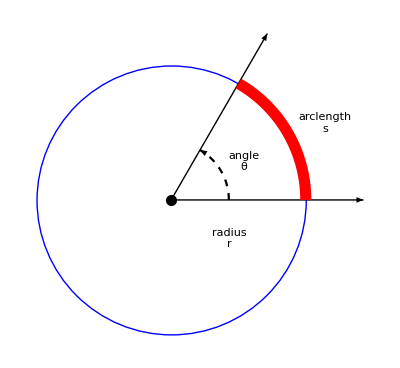

{radian-measure-angle.pdf,radian-measure-angle.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
Show[
Graphics[{Blue,Thick,Circle[{0,0},.7]}],
Graphics[Arrow[{{0,0},{Cos[Pi/3],Sin[Pi/3]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{0.7Cos[t],0.7Sin[t]},{t,0,Pi/3},PlotStyle->{Red,Thickness[0.02]}],
ParametricPlot[{0.3Cos[t],0.3Sin[t]},{t,0,Pi/3},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Epilog->{
Style[Text["angle\nθ",{0.38,0.2}],20],
Style[Text["radius\nr",{0.3,-0.2}],20],
Style[Text["arclength\ns",{0.8,0.4}],20]
}
]
Export[{"radian-measure-angle.pdf","radian-measure-angle.svg"},%]
```

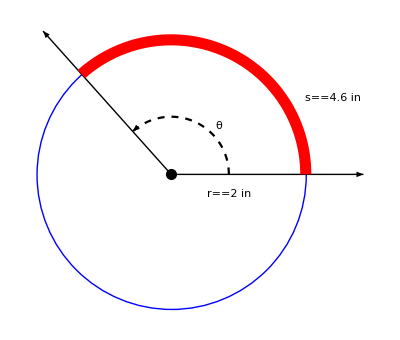

{radian-measure-angle-example.pdf,radian-measure-angle-example.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
Unset[r]
theta=2.3;
Show[
Graphics[{Blue,Thick,Circle[{0,0},.7]}],
Graphics[Arrow[{{0,0},{Cos[theta],Sin[theta]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{0.7Cos[t],0.7Sin[t]},{t,theta,0},PlotStyle->{Red,Thickness[0.02]}],
ParametricPlot[{0.3Cos[t],0.3Sin[t]},{t,theta,0},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0,0.05}],Arrow[x]],
Epilog->{
Style[Text[HoldForm[θ],{0.25,0.25}],20],
Style[Text[TraditionalForm[r==Quantity[2,"Inch"]],{0.3,-0.1}],20],
Style[Text[s==Quantity[4.6,"Inch"],{0.84,0.4}],20]
}
]
Export[{"radian-measure-angle-example.pdf","radian-measure-angle-example.svg"},%]
```

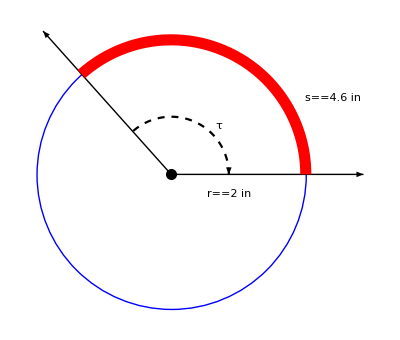

{radian-measure-angle-example-negative.pdf,radian-measure-angle-example-negative.svg}

```mathematica
SetDirectory[NotebookDirectory[]];
theta=2.3;
Show[
Graphics[{Blue,Thick,Circle[{0,0},.7]}],
Graphics[Arrow[{{0,0},{Cos[theta],Sin[theta]}}]],
Graphics[Arrow[{{0,0},{1,0}}]],
Graphics[{PointSize[0.02],Point[{0,0}]}],
ParametricPlot[{0.7Cos[t],0.7Sin[t]},{t,0,theta},PlotStyle->{Red,Thickness[0.02]}],
ParametricPlot[{0.3Cos[t],0.3Sin[t]},{t,0,theta},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{-0.05,0}],Arrow[x]],
Epilog->{
Style[Text[τ,{0.25,0.25}],20],
Style[Text[r==Quantity[2,"Inch"],{0.3,-0.1}],20],
Style[Text[s==Quantity[4.6,"Inch"],{0.84,0.4}],20]
}
]
Export[{"radian-measure-angle-example-negative.pdf","radian-measure-angle-example-negative.svg"},%]
```

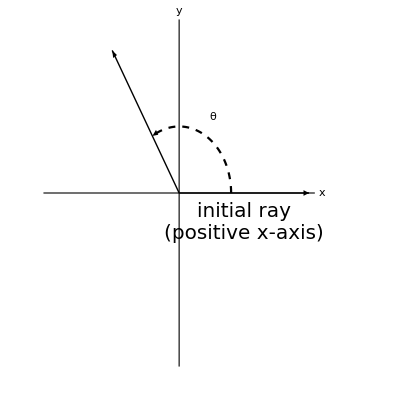

```mathematica
r=4;
θ=121*Degree;
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Cos[t],Sin[t]}2,{t,0,θ},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+1.4}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18],
Epilog->{Text[Style["initial ray\n(positive x-axis)",20],{2.5,-0.9}]}]
Export[{"standard-position-q2.pdf","standard-position-q2.svg"},%];
```

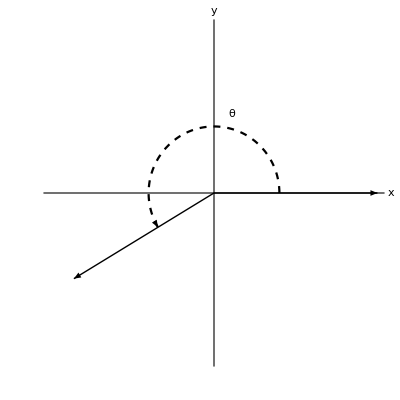

```mathematica
r=4;
θ=121*Degree+90*Degree;
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Cos[t],Sin[t]}2,{t,0,θ},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{.05}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+1.4}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"standard-position-q3.pdf","standard-position-q3.svg"},%];
```

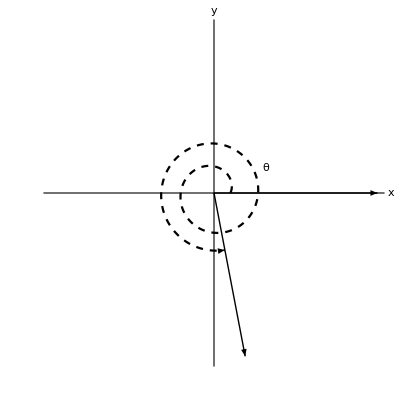

```mathematica
r=4;
θ=121*Degree+520*Degree;
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Sqrt[t+1]Cos[t]/10,Sqrt[t+1]Sin[t]/10}5,{t,0,θ},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+1.4}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"standard-position-q4.pdf","standard-position-q4.svg"},%];
```

```mathematica
Quit[]
```

/Users/ant/Sites/JumpStartIM/assets/images/trig

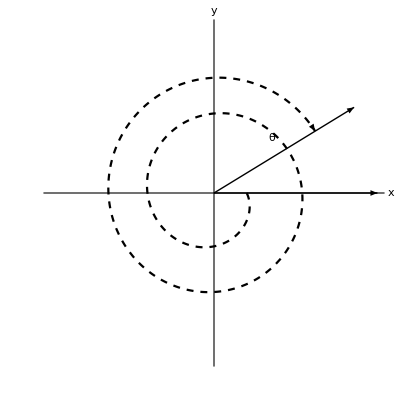

```mathematica
SetDirectory[NotebookDirectory[]]
r=4;
θ=+(121*Degree+720*Degree-90*Degree);
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Sqrt[t+1]Cos[-t]/20,Sqrt[t+1]Sin[-t]/20}20,{t,0,θ-2*31*Degree},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+1.4}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"standard-position-q1.pdf","standard-position-q1.svg"},%];
```

```mathematica
""
```

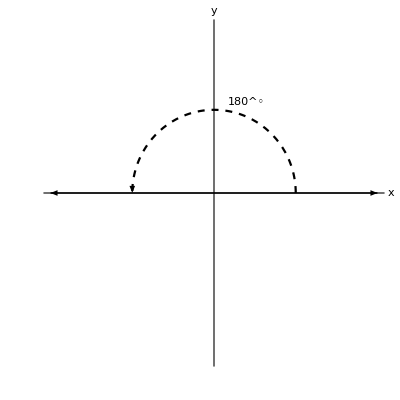

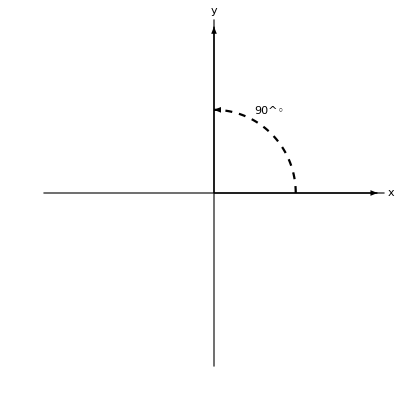

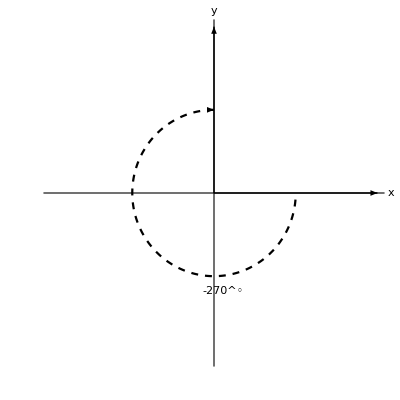

```mathematica
r=3;
θ=180*Degree;
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Cos[t],Sin[t]}2,{t,0,θ},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[180^◦],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+1.4}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"standard-position-180.pdf","standard-position-180.svg"},%];
r=3;
θ=90*Degree;
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Cos[t],Sin[t]}2,{t,0,θ},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{0.05}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[90^◦],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+1.4}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"standard-position-90.pdf","standard-position-90.svg"},%];r=3;
θ=-270*Degree;
Show[
Plot[{},{x,-4,4}],
ParametricPlot[{Cos[t],Sin[t]}2,{t,0,θ},PlotStyle->{Black,Dashed}]/.
Line[x_]:>Sequence[Arrowheads[{-0.05,0}],Arrow[x]],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Text[Style[HoldForm[-270^◦],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]-1.8}]}],Ticks->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"standard-position-m270.pdf","standard-position-m270.svg"},%];
```

```mathematica
-9*90
```

-810

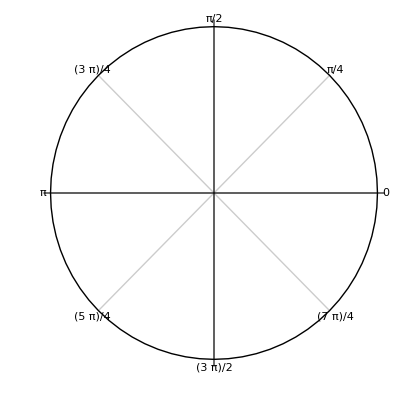

```mathematica
θ=Pi/4;
Show[PolarPlot[{},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],{}},PolarAxes->Automatic]]
Export[{"sketch-8.pdf","sketch-8.svg"},%];
```

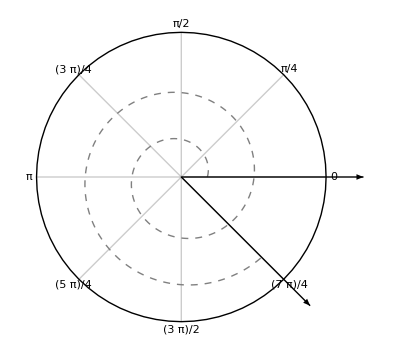

```mathematica
θ=15Pi/4;
Show[PolarPlot[{t/7+0.5},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},3.5{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},3.5{Cos[θ],Sin[θ]}}]}]]
Export[{"sketch-8-2.pdf","sketch-8-2.svg"},%];
```

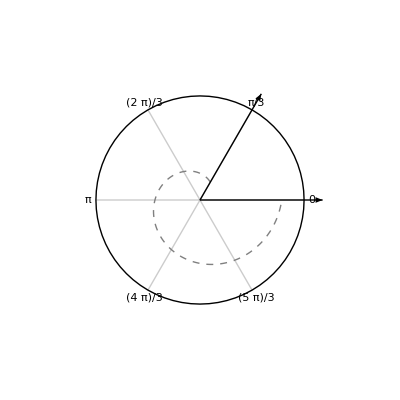

```mathematica
θ=-5Pi/3;
Show[PolarPlot[{t/7+1},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/3,Pi/3}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},1.5{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},1.5{Cos[θ],Sin[θ]}}]}],
PlotRange->{{-2,2},{-2,2}}]
Export[{"sketch-8-3.pdf","sketch-8-3.svg"},%];
```

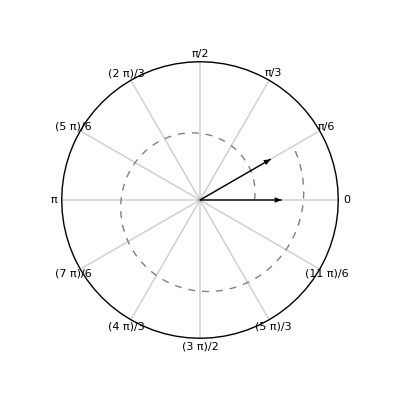

```mathematica
θ=13Pi/6;
Show[PolarPlot[{t/7+1},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/6,Pi/6}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/6,Pi/6}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},1.5{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},1.5{Cos[θ],Sin[θ]}}]}],
PlotRange->{{-3,3},{-3,3}}]
Export[{"sketch-8-6.pdf","sketch-8-6.svg"},%];
```

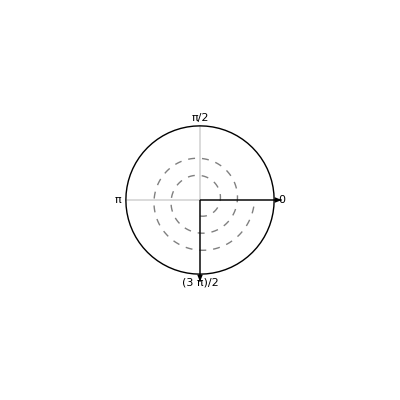

```mathematica
θ=-810*Degree;
Show[PolarPlot[{t/20+1},{t,θ,0},PlotStyle->{Thick,Dashed,Gray},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/2,Pi/2}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/2,Pi/2}],{}},PolarAxes->Automatic],
Graphics[{Arrow[{{0,0},1.5{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},1.5{Cos[θ],Sin[θ]}}]}],
PlotRange->{{-3,3},{-3,3}}]
Export[{"sketch-quad.pdf","sketch-quad.svg"},%];
```

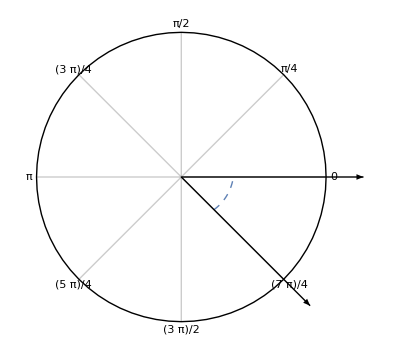

```mathematica
θ=15Pi/4;
Show[
PolarPlot[{t/7+0.5},{t,θ,0},PlotStyle->{Thick,Dashed,Opacity[0]},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],{}},PolarAxes->Automatic],
PolarPlot[{t/7+1},{t,0,-Pi/4},PlotStyle->{Thick,Dashed}],
Graphics[{Arrow[{{0,0},3.5{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},3.5{Cos[θ],Sin[θ]}}]}]]
Export[{"sketch-8-2-ctm.pdf","sketch-8-2-ctm.svg"},%];
```

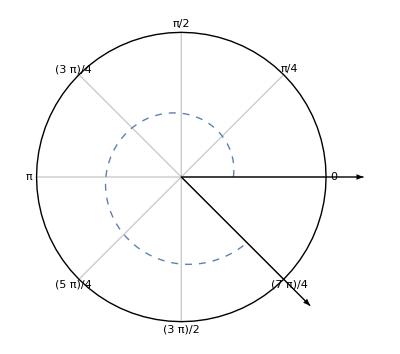

```mathematica
θ=15Pi/4;
Show[
PolarPlot[{t/7+0.5},{t,θ,0},PlotStyle->{Thick,Dashed,Opacity[0]},Ticks->None,PolarTicks->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],Automatic},
PolarGridLines->{Table[i,{i,0,2 Pi-Pi/4,Pi/4}],{}},PolarAxes->Automatic],
PolarPlot[{t/7+1},{t,0,7Pi/4},PlotStyle->{Thick,Dashed}],
Graphics[{Arrow[{{0,0},3.5{Cos[0],Sin[0]}}]}],
Graphics[{Arrow[{{0,0},3.5{Cos[θ],Sin[θ]}}]}]]
Export[{"sketch-8-2-ctp.pdf","sketch-8-2-ctp.svg"},%];
```

121 °

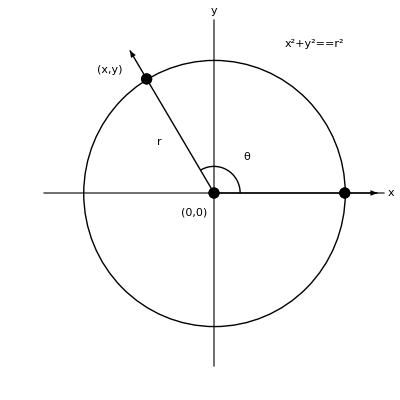

{trig-function-defn.pdf,trig-function-defn.svg}

```mathematica
r=4;
θ=121*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2-0.4,(r+1) Sin[θ]/2-0.6}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.6,(r+1) Sin[θ]-0.6}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],Large,Italic],{(r+1) Cos[θ/2]+0.6,(r+1) Sin[θ]+0.2}]}],
Graphics[{Text[Style["(0,0)",Large,Italic],{0-0.6,0-0.6}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"trig-function-defn.pdf","trig-function-defn.svg"},%]
```

31 °

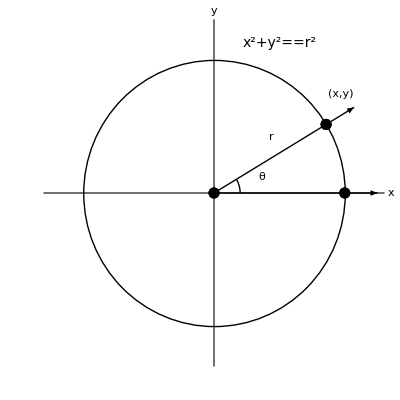

{trig-function-defn-q1.pdf,trig-function-defn-q1.svg}

```mathematica
r=4;
θ=121*Degree-90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2-0.4,(r+1) Sin[θ]/2+0.4}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.4,(r+1) Sin[θ]+0.4}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"trig-function-defn-q1.pdf","trig-function-defn-q1.svg"},%]
```

121 °

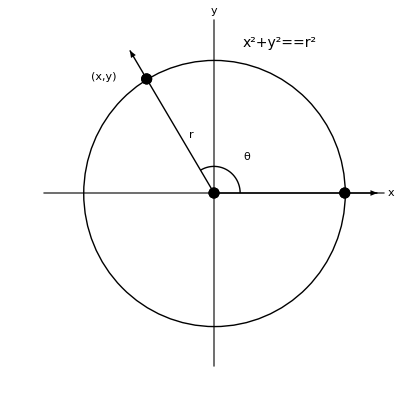

{trig-function-defn-q2.pdf,trig-function-defn-q2.svg}

```mathematica
r=4;
θ=121*Degree-0*90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2+0.6,(r+1) Sin[θ]/2-0.4}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]-0.8,(r+1) Sin[θ]-0.8}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"trig-function-defn-q2.pdf","trig-function-defn-q2.svg"},%]
```

211 °

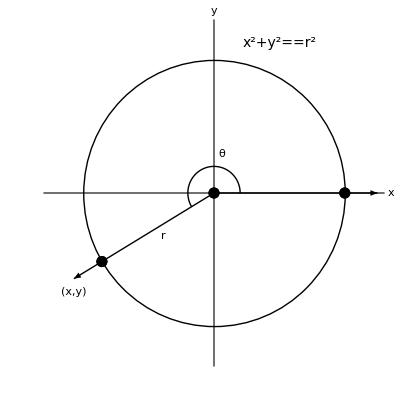

{trig-function-defn-q3.pdf,trig-function-defn-q3.svg}

```mathematica
r=4;
θ=121*Degree+1*90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2+0.6,(r+1) Sin[θ]/2}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ],(r+1) Sin[θ]-0.4}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.5,0.2(r+1) Sin[θ/2]+0.2}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"trig-function-defn-q3.pdf","trig-function-defn-q3.svg"},%]
```

301 °

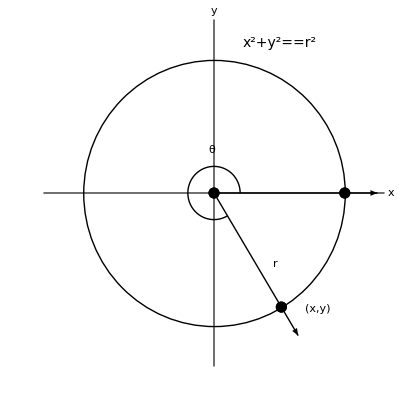

{trig-function-defn-q4.pdf,trig-function-defn-q4.svg}

```mathematica
r=4;
θ=121*Degree+2*90*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{0,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style[HoldForm[r],Large,Italic],{(r+1) Cos[θ]/2+0.6,(r+1) Sin[θ]/2}]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{(r+1) Cos[θ]+0.6,(r+1) Sin[θ]+0.8}]}],
Graphics[{Text[Style[HoldForm[x^2+y^2==r^2],14,Italic],{2,4.5}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[HoldForm[θ],Large],{0.2(r+1) Cos[θ/2]+0.8,0.2(r+1) Sin[θ/2]+0.8}]}],
Ticks->None,GridLines->None,
PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"trig-function-defn-q4.pdf","trig-function-defn-q4.svg"},%]
```

207 °

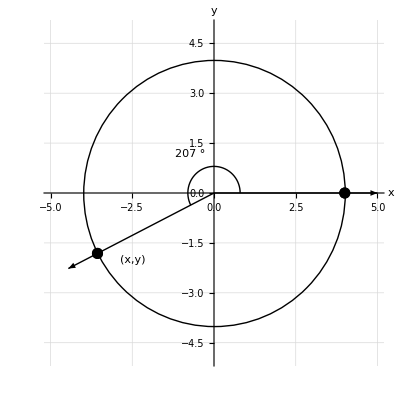

{circle.pdf,circle.svg}

```mathematica
r=4;
θ=207*Degree
Show[
ListPlot[{{r Cos[θ],r Sin[θ]}},PlotStyle->{Black,PointSize[0.02]}],
ListPlot[{{r ,0}},PlotStyle->{Black,PointSize[0.02]}],
Graphics[{Text[Style["(x,y)",Large,Italic],{-2.5,-2}]}],
Graphics[{Arrow[{{0,0},{(r+1) Cos[θ],(r+1) Sin[θ]}}]}],
Graphics[{Arrow[{{0,0},{(r+1) ,0}}]}],
Graphics[{Circle[{0,0},r]}],
Graphics[{Circle[{0,0},0.2r,{0,θ}]}],
Graphics[{Text[Style[θ,Large],{0.2(r+1) Cos[θ/2]-0.5,0.2(r+1) Sin[θ/2]+0.2}]}],

PlotRange->{{-(r+1),r+1},{-(r+1),r+1}},GridLines->Automatic,AspectRatio->1,AxesLabel->{"x","y"},AxesStyle->Directive[18]]
Export[{"circle.pdf","circle.svg"},%]
```